# Triple Pendulum With Excitation

-Graphics-

```mathematica
ClearAll["Global`*"]
$Assumptions={Subscript[l, _]>0&&Subscript[m, _]>0}
```

{l__>0&&m__>0}

## Lagrange's Equations of Motion

Assuming x axis point downward and y axis to the right, we can define position coordinates for all masses :

```mathematica
Subscript[x, 0][t]=0; Do[Print[Subscript[x, k][t_]=Subscript[x, k-1][t]+Subscript[l, k] Cos[Subscript[θ, k][t]]],{k,3}]
Subscript[y, 0][t]=0; Do[Print[Subscript[y, k][t_]=Subscript[y, k-1][t]+Subscript[l, k] Sin[Subscript[θ, k][t]]],{k,3}]
```

Cos[θ_1[t]] l_1

Cos[θ_1[t]] l_1+Cos[θ_2[t]] l_2

Cos[θ_1[t]] l_1+Cos[θ_2[t]] l_2+Cos[θ_3[t]] l_3

Sin[θ_1[t]] l_1

Sin[θ_1[t]] l_1+Sin[θ_2[t]] l_2

Sin[θ_1[t]] l_1+Sin[θ_2[t]] l_2+Sin[θ_3[t]] l_3

Define kinetic energy of a system:

```mathematica
T=Sum[1/2 Subscript[m, k](D[Subscript[x, k][t],t]^2+D[Subscript[y, k][t],t]^2),{k,3}]//Simplify
```

1/2 (l_1^2 m_1 θ_1'[t]^2+m_2 (l_1^2 θ_1'[t]^2+2 Cos[θ_1[t]-θ_2[t]] l_1 l_2 θ_1'[t] θ_2'[t]+l_2^2 θ_2'[t]^2)+m_3 ((Cos[θ_1[t]] l_1 θ_1'[t]+Cos[θ_2[t]] l_2 θ_2'[t]+Cos[θ_3[t]] l_3 θ_3'[t])^2+(Sin[θ_1[t]] l_1 θ_1'[t]+Sin[θ_2[t]] l_2 θ_2'[t]+Sin[θ_3[t]] l_3 θ_3'[t])^2))

Define potential energy of a system:

```mathematica
V=Sum[-{Subscript[m, k] g,0}.{ Subscript[x, k][t],Subscript[y, k][t]},{k,3}]//ExpandAll
```

-g Cos[θ_1[t]] l_1 m_1-g Cos[θ_1[t]] l_1 m_2-g Cos[θ_2[t]] l_2 m_2-g Cos[θ_1[t]] l_1 m_3-g Cos[θ_2[t]] l_2 m_3-g Cos[θ_3[t]] l_3 m_3

```mathematica
Lg=T-V
```

g Cos[θ_1[t]] l_1 m_1+g Cos[θ_1[t]] l_1 m_2+g Cos[θ_2[t]] l_2 m_2+g Cos[θ_1[t]] l_1 m_3+g Cos[θ_2[t]] l_2 m_3+g Cos[θ_3[t]] l_3 m_3+1/2 (l_1^2 m_1 θ_1'[t]^2+m_2 (l_1^2 θ_1'[t]^2+2 Cos[θ_1[t]-θ_2[t]] l_1 l_2 θ_1'[t] θ_2'[t]+l_2^2 θ_2'[t]^2)+m_3 ((Cos[θ_1[t]] l_1 θ_1'[t]+Cos[θ_2[t]] l_2 θ_2'[t]+Cos[θ_3[t]] l_3 θ_3'[t])^2+(Sin[θ_1[t]] l_1 θ_1'[t]+Sin[θ_2[t]] l_2 θ_2'[t]+Sin[θ_3[t]] l_3 θ_3'[t])^2))

Define virtual work of a system:

```mathematica
δW = {0,F[t]}. D[{Subscript[x, 3][t],Subscript[y, 3][t]},t]/.Subscript[θ, n_]'[t]-> Subscript[δθ, n]//Expand
```

Cos[θ_1[t]] F[t] l_1 δθ_1+Cos[θ_2[t]] F[t] l_2 δθ_2+Cos[θ_3[t]] F[t] l_3 δθ_3

Assemble equations of motion:

```mathematica
Scan[Print[
Subscript[eq, #]=Expand[
D[D[Lg,Subscript[θ, #]'[t]],t]-D[Lg,Subscript[θ, #][t]]==Coefficient[δW,Subscript[δθ, #]]
]] &, {1,2,3}]
```

g Sin[θ_1[t]] l_1 m_1+g Sin[θ_1[t]] l_1 m_2+g Sin[θ_1[t]] l_1 m_3+Sin[θ_1[t]-θ_2[t]] l_1 l_2 m_2 θ_2'[t]^2+Cos[θ_2[t]] Sin[θ_1[t]] l_1 l_2 m_3 θ_2'[t]^2-Cos[θ_1[t]] Sin[θ_2[t]] l_1 l_2 m_3 θ_2'[t]^2+Cos[θ_3[t]] Sin[θ_1[t]] l_1 l_3 m_3 θ_3'[t]^2-Cos[θ_1[t]] Sin[θ_3[t]] l_1 l_3 m_3 θ_3'[t]^2+l_1^2 m_1 θ_1''[t]+l_1^2 m_2 θ_1''[t]+Cos[θ_1[t]]^2 l_1^2 m_3 θ_1''[t]+Sin[θ_1[t]]^2 l_1^2 m_3 θ_1''[t]+Cos[θ_1[t]-θ_2[t]] l_1 l_2 m_2 θ_2''[t]+Cos[θ_1[t]] Cos[θ_2[t]] l_1 l_2 m_3 θ_2''[t]+Sin[θ_1[t]] Sin[θ_2[t]] l_1 l_2 m_3 θ_2''[t]+Cos[θ_1[t]] Cos[θ_3[t]] l_1 l_3 m_3 θ_3''[t]+Sin[θ_1[t]] Sin[θ_3[t]] l_1 l_3 m_3 θ_3''[t]==Cos[θ_1[t]] F[t] l_1

g Sin[θ_2[t]] l_2 m_2+g Sin[θ_2[t]] l_2 m_3-Sin[θ_1[t]-θ_2[t]] l_1 l_2 m_2 θ_1'[t]^2-Cos[θ_2[t]] Sin[θ_1[t]] l_1 l_2 m_3 θ_1'[t]^2+Cos[θ_1[t]] Sin[θ_2[t]] l_1 l_2 m_3 θ_1'[t]^2+Cos[θ_3[t]] Sin[θ_2[t]] l_2 l_3 m_3 θ_3'[t]^2-Cos[θ_2[t]] Sin[θ_3[t]] l_2 l_3 m_3 θ_3'[t]^2+Cos[θ_1[t]-θ_2[t]] l_1 l_2 m_2 θ_1''[t]+Cos[θ_1[t]] Cos[θ_2[t]] l_1 l_2 m_3 θ_1''[t]+Sin[θ_1[t]] Sin[θ_2[t]] l_1 l_2 m_3 θ_1''[t]+l_2^2 m_2 θ_2''[t]+Cos[θ_2[t]]^2 l_2^2 m_3 θ_2''[t]+Sin[θ_2[t]]^2 l_2^2 m_3 θ_2''[t]+Cos[θ_2[t]] Cos[θ_3[t]] l_2 l_3 m_3 θ_3''[t]+Sin[θ_2[t]] Sin[θ_3[t]] l_2 l_3 m_3 θ_3''[t]==Cos[θ_2[t]] F[t] l_2

g Sin[θ_3[t]] l_3 m_3-Cos[θ_3[t]] Sin[θ_1[t]] l_1 l_3 m_3 θ_1'[t]^2+Cos[θ_1[t]] Sin[θ_3[t]] l_1 l_3 m_3 θ_1'[t]^2-Cos[θ_3[t]] Sin[θ_2[t]] l_2 l_3 m_3 θ_2'[t]^2+Cos[θ_2[t]] Sin[θ_3[t]] l_2 l_3 m_3 θ_2'[t]^2+Cos[θ_1[t]] Cos[θ_3[t]] l_1 l_3 m_3 θ_1''[t]+Sin[θ_1[t]] Sin[θ_3[t]] l_1 l_3 m_3 θ_1''[t]+Cos[θ_2[t]] Cos[θ_3[t]] l_2 l_3 m_3 θ_2''[t]+Sin[θ_2[t]] Sin[θ_3[t]] l_2 l_3 m_3 θ_2''[t]+Cos[θ_3[t]]^2 l_3^2 m_3 θ_3''[t]+Sin[θ_3[t]]^2 l_3^2 m_3 θ_3''[t]==Cos[θ_3[t]] F[t] l_3

## Equilibrium Points

```mathematica
EqEqs={Subscript[eq, 1],Subscript[eq, 2],Subscript[eq, 3]}/.{Subscript[θ, _]'[t]->0,Subscript[θ, _]''[t]->0,F[t]->0}
```

{g Sin[θ_1[t]] l_1 m_1+g Sin[θ_1[t]] l_1 m_2+g Sin[θ_1[t]] l_1 m_3==0,g Sin[θ_2[t]] l_2 m_2+g Sin[θ_2[t]] l_2 m_3==0,g Sin[θ_3[t]] l_3 m_3==0}

```mathematica
EqSols=Solve[EqEqs,{Subscript[θ, 1][t],Subscript[θ, 2][t],Subscript[θ, 3][t]}]
```

{{θ_1[t]→ConditionalExpression[2 π C[1], C[1]∈ℤ],θ_2[t]→ConditionalExpression[2 π C[2], C[2]∈ℤ],θ_3[t]→ConditionalExpression[2 π C[3], C[3]∈ℤ]},{θ_1[t]→ConditionalExpression[2 π C[1], C[1]∈ℤ],θ_2[t]→ConditionalExpression[2 π C[2], C[2]∈ℤ],θ_3[t]→ConditionalExpression[π+2 π C[3], C[3]∈ℤ]},{θ_1[t]→ConditionalExpression[2 π C[1], C[1]∈ℤ],θ_2[t]→ConditionalExpression[π+2 π C[2], C[2]∈ℤ],θ_3[t]→ConditionalExpression[2 π C[3], C[3]∈ℤ]},{θ_1[t]→ConditionalExpression[2 π C[1], C[1]∈ℤ],θ_2[t]→ConditionalExpression[π+2 π C[2], C[2]∈ℤ],θ_3[t]→ConditionalExpression[π+2 π C[3], C[3]∈ℤ]},{θ_1[t]→ConditionalExpression[π+2 π C[1], C[1]∈ℤ],θ_2[t]→ConditionalExpression[2 π C[2], C[2]∈ℤ],θ_3[t]→ConditionalExpression[2 π C[3], C[3]∈ℤ]},{θ_1[t]→ConditionalExpression[π+2 π C[1], C[1]∈ℤ],θ_2[t]→ConditionalExpression[2 π C[2], C[2]∈ℤ],θ_3[t]→ConditionalExpression[π+2 π C[3], C[3]∈ℤ]},{θ_1[t]→ConditionalExpression[π+2 π C[1], C[1]∈ℤ],θ_2[t]→ConditionalExpression[π+2 π C[2], C[2]∈ℤ],θ_3[t]→ConditionalExpression[2 π C[3], C[3]∈ℤ]},{θ_1[t]→ConditionalExpression[π+2 π C[1], C[1]∈ℤ],θ_2[t]→ConditionalExpression[π+2 π C[2], C[2]∈ℤ],θ_3[t]→ConditionalExpression[π+2 π C[3], C[3]∈ℤ]}}

```mathematica
EqSols=EqSols/.{C[_]->0}
```

{{θ_1[t]→0,θ_2[t]→0,θ_3[t]→0},{θ_1[t]→0,θ_2[t]→0,θ_3[t]→π},{θ_1[t]→0,θ_2[t]→π,θ_3[t]→0},{θ_1[t]→0,θ_2[t]→π,θ_3[t]→π},{θ_1[t]→π,θ_2[t]→0,θ_3[t]→0},{θ_1[t]→π,θ_2[t]→0,θ_3[t]→π},{θ_1[t]→π,θ_2[t]→π,θ_3[t]→0},{θ_1[t]→π,θ_2[t]→π,θ_3[t]→π}}

The only stable equilibrium is the first solution (0,0,0). To see this you can linearize the equations about one of the other equilibrium points (say (0,0,π)).

### Linearized Equations of Motion

Prepare for linearization about a general equilibrium point (θe_1, θe_2, θe_3) (this is a trick to do multivariate Taylor expansion):

```mathematica
subs=Join[
Table[Subscript[θ, k][t]-> Subscript[θe, k]+q Subscript[θ, k][t],{k,3}],Table[Subscript[θ, k]'[t]-> q Subscript[θ, k]'[t],{k,3}],
Table[Subscript[θ, k]''[t]-> q Subscript[θ, k]''[t],{k,3}]]
```

{θ_1[t]→θe_1+q θ_1[t],θ_2[t]→θe_2+q θ_2[t],θ_3[t]→θe_3+q θ_3[t],θ_1'[t]→q θ_1'[t],θ_2'[t]→q θ_2'[t],θ_3'[t]→q θ_3'[t],θ_1''[t]→q θ_1''[t],θ_2''[t]→q θ_2''[t],θ_3''[t]→q θ_3''[t]}

Linearize equations (use the trick):

```mathematica
Do[Print[Subscript[Eq, k]=Normal[Series[Subscript[eq, k]/.subs,{q,0,1}]]/.q-> 1],{k,3}]
```

g Sin[θe_1] l_1 m_1+g Sin[θe_1] l_1 m_2+g Sin[θe_1] l_1 m_3+g Cos[θe_1] l_1 m_1 θ_1[t]+g Cos[θe_1] l_1 m_2 θ_1[t]+g Cos[θe_1] l_1 m_3 θ_1[t]+l_1^2 m_1 θ_1''[t]+l_1^2 m_2 θ_1''[t]+Cos[θe_1]^2 l_1^2 m_3 θ_1''[t]+Sin[θe_1]^2 l_1^2 m_3 θ_1''[t]+Cos[θe_1-θe_2] l_1 l_2 m_2 θ_2''[t]+Cos[θe_1] Cos[θe_2] l_1 l_2 m_3 θ_2''[t]+Sin[θe_1] Sin[θe_2] l_1 l_2 m_3 θ_2''[t]+Cos[θe_1] Cos[θe_3] l_1 l_3 m_3 θ_3''[t]+Sin[θe_1] Sin[θe_3] l_1 l_3 m_3 θ_3''[t]==Cos[θe_1] F[t] l_1-F[t] Sin[θe_1] l_1 θ_1[t]

g Sin[θe_2] l_2 m_2+g Sin[θe_2] l_2 m_3+g Cos[θe_2] l_2 m_2 θ_2[t]+g Cos[θe_2] l_2 m_3 θ_2[t]+Cos[θe_1-θe_2] l_1 l_2 m_2 θ_1''[t]+Cos[θe_1] Cos[θe_2] l_1 l_2 m_3 θ_1''[t]+Sin[θe_1] Sin[θe_2] l_1 l_2 m_3 θ_1''[t]+l_2^2 m_2 θ_2''[t]+Cos[θe_2]^2 l_2^2 m_3 θ_2''[t]+Sin[θe_2]^2 l_2^2 m_3 θ_2''[t]+Cos[θe_2] Cos[θe_3] l_2 l_3 m_3 θ_3''[t]+Sin[θe_2] Sin[θe_3] l_2 l_3 m_3 θ_3''[t]==Cos[θe_2] F[t] l_2-F[t] Sin[θe_2] l_2 θ_2[t]

g Sin[θe_3] l_3 m_3+g Cos[θe_3] l_3 m_3 θ_3[t]+Cos[θe_1] Cos[θe_3] l_1 l_3 m_3 θ_1''[t]+Sin[θe_1] Sin[θe_3] l_1 l_3 m_3 θ_1''[t]+Cos[θe_2] Cos[θe_3] l_2 l_3 m_3 θ_2''[t]+Sin[θe_2] Sin[θe_3] l_2 l_3 m_3 θ_2''[t]+Cos[θe_3]^2 l_3^2 m_3 θ_3''[t]+Sin[θe_3]^2 l_3^2 m_3 θ_3''[t]==Cos[θe_3] F[t] l_3-F[t] Sin[θe_3] l_3 θ_3[t]

Use simple parameter assignments as given in the problem:

```mathematica
subs=Join[Table[Subscript[m, k]-> M,{k,3}],Table[Subscript[l, k]-> L,{k,3}]]
```

{m_1→M,m_2→M,m_3→M,l_1→L,l_2→L,l_3→L}

Then the linearized equations of motions about some equilibrium point (θe_1, θe_2, θe_3)  are

```mathematica
Do[Print[Subscript[Eq, k]=(Subscript[Eq, k]/.subs)],{k,3}]
```

3 g L M Sin[θe_1]+3 g L M Cos[θe_1] θ_1[t]+2 L^2 M θ_1''[t]+L^2 M Cos[θe_1]^2 θ_1''[t]+L^2 M Sin[θe_1]^2 θ_1''[t]+L^2 M Cos[θe_1-θe_2] θ_2''[t]+L^2 M Cos[θe_1] Cos[θe_2] θ_2''[t]+L^2 M Sin[θe_1] Sin[θe_2] θ_2''[t]+L^2 M Cos[θe_1] Cos[θe_3] θ_3''[t]+L^2 M Sin[θe_1] Sin[θe_3] θ_3''[t]==L Cos[θe_1] F[t]-L F[t] Sin[θe_1] θ_1[t]

2 g L M Sin[θe_2]+2 g L M Cos[θe_2] θ_2[t]+L^2 M Cos[θe_1-θe_2] θ_1''[t]+L^2 M Cos[θe_1] Cos[θe_2] θ_1''[t]+L^2 M Sin[θe_1] Sin[θe_2] θ_1''[t]+L^2 M θ_2''[t]+L^2 M Cos[θe_2]^2 θ_2''[t]+L^2 M Sin[θe_2]^2 θ_2''[t]+L^2 M Cos[θe_2] Cos[θe_3] θ_3''[t]+L^2 M Sin[θe_2] Sin[θe_3] θ_3''[t]==L Cos[θe_2] F[t]-L F[t] Sin[θe_2] θ_2[t]

g L M Sin[θe_3]+g L M Cos[θe_3] θ_3[t]+L^2 M Cos[θe_1] Cos[θe_3] θ_1''[t]+L^2 M Sin[θe_1] Sin[θe_3] θ_1''[t]+L^2 M Cos[θe_2] Cos[θe_3] θ_2''[t]+L^2 M Sin[θe_2] Sin[θe_3] θ_2''[t]+L^2 M Cos[θe_3]^2 θ_3''[t]+L^2 M Sin[θe_3]^2 θ_3''[t]==L Cos[θe_3] F[t]-L F[t] Sin[θe_3] θ_3[t]

### Stability of Equilibrium Points

To evaluate the stability of the equilibrium points, we need to find the eigenvalues of the Jacobian. If all have nonpositive real parts then the equilibrium is stable, otherwise it is unstable.

```mathematica
Jsols=Solve[{Subscript[Eq, 1],Subscript[Eq, 2],Subscript[Eq, 3]},{Subscript[θ, 1]''[t],Subscript[θ, 2]''[t],Subscript[θ, 3]''[t]}][[1]]/.{F[t]->0}//Simplify
```

{θ_1''[t]→-1/(2 L (-5+2 Cos[2 θe_1-2 θe_2]+Cos[2 θe_2-2 θe_3]))g (-10 Sin[θe_1]-4 Sin[θe_1-2 θe_2]+Sin[θe_1+2 θe_2-2 θe_3]+Sin[θe_1-2 θe_2+2 θe_3]+6 Cos[θe_1] (-3+Cos[2 θe_2-2 θe_3]) θ_1[t]-4 Cos[θe_2] (-3 Cos[θe_1-θe_2]+Cos[θe_1+θe_2-2 θe_3]) θ_2[t]+2 Cos[θe_1] θ_3[t]-2 Cos[θe_1-2 θe_2] θ_3[t]+2 Cos[θe_1-2 θe_3] θ_3[t]-2 Cos[θe_1-2 θe_2+2 θe_3] θ_3[t]),θ_2''[t]→1/(2 L (-5+2 Cos[2 θe_1-2 θe_2]+Cos[2 θe_2-2 θe_3]))g (-7 Sin[2 θe_1-θe_2]+7 Sin[θe_2]+Sin[θe_2-2 θe_3]+Sin[2 θe_1+θe_2-2 θe_3]+6 Cos[θe_1] (-3 Cos[θe_1-θe_2]+Cos[θe_1+θe_2-2 θe_3]) θ_1[t]-4 Cos[θe_2] (-5+Cos[2 θe_1-2 θe_3]) θ_2[t]+2 Cos[2 θe_1-θe_2] θ_3[t]-4 Cos[θe_2] θ_3[t]+2 Cos[2 θe_1-θe_2-2 θe_3] θ_3[t]-4 Cos[θe_2-2 θe_3] θ_3[t]),θ_3''[t]→(g (-Sin[2 θe_1-θe_3]-Sin[2 θe_2-θe_3]+Sin[θe_3]+Sin[2 θe_1-2 θe_2+θe_3]+12 Cos[θe_1] Sin[θe_1-θe_2] Sin[θe_2-θe_3] θ_1[t]+4 Cos[θe_2] (Cos[2 θe_1-θe_2-θe_3]-2 Cos[θe_2-θe_3]) θ_2[t]-2 Cos[2 θe_1-2 θe_2-θe_3] θ_3[t]+8 Cos[θe_3] θ_3[t]-2 Cos[2 θe_1-2 θe_2+θe_3] θ_3[t]))/(L (-5+2 Cos[2 θe_1-2 θe_2]+Cos[2 θe_2-2 θe_3]))}

Then the equations of motion can be written is a state space form with respect to a new state variable

```mathematica
z=Join[Table[Subscript[θ, k][t],{k,3}],Table[Subscript[θ, k]'[t],{k,3}]]
```

{θ_1[t],θ_2[t],θ_3[t],θ_1'[t],θ_2'[t],θ_3'[t]}

The right hand side of the corresponding equation z’=Dz is given by

```mathematica
Dz=Join[z[[4;;6]],Jsols[[1;;3,2]]]
```

{θ_1'[t],θ_2'[t],θ_3'[t],-1/(2 L (-5+2 Cos[2 θe_1-2 θe_2]+Cos[2 θe_2-2 θe_3]))g (-10 Sin[θe_1]-4 Sin[θe_1-2 θe_2]+Sin[θe_1+2 θe_2-2 θe_3]+Sin[θe_1-2 θe_2+2 θe_3]+6 Cos[θe_1] (-3+Cos[2 θe_2-2 θe_3]) θ_1[t]-4 Cos[θe_2] (-3 Cos[θe_1-θe_2]+Cos[θe_1+θe_2-2 θe_3]) θ_2[t]+2 Cos[θe_1] θ_3[t]-2 Cos[θe_1-2 θe_2] θ_3[t]+2 Cos[θe_1-2 θe_3] θ_3[t]-2 Cos[θe_1-2 θe_2+2 θe_3] θ_3[t]),1/(2 L (-5+2 Cos[2 θe_1-2 θe_2]+Cos[2 θe_2-2 θe_3]))g (-7 Sin[2 θe_1-θe_2]+7 Sin[θe_2]+Sin[θe_2-2 θe_3]+Sin[2 θe_1+θe_2-2 θe_3]+6 Cos[θe_1] (-3 Cos[θe_1-θe_2]+Cos[θe_1+θe_2-2 θe_3]) θ_1[t]-4 Cos[θe_2] (-5+Cos[2 θe_1-2 θe_3]) θ_2[t]+2 Cos[2 θe_1-θe_2] θ_3[t]-4 Cos[θe_2] θ_3[t]+2 Cos[2 θe_1-θe_2-2 θe_3] θ_3[t]-4 Cos[θe_2-2 θe_3] θ_3[t]),(g (-Sin[2 θe_1-θe_3]-Sin[2 θe_2-θe_3]+Sin[θe_3]+Sin[2 θe_1-2 θe_2+θe_3]+12 Cos[θe_1] Sin[θe_1-θe_2] Sin[θe_2-θe_3] θ_1[t]+4 Cos[θe_2] (Cos[2 θe_1-θe_2-θe_3]-2 Cos[θe_2-θe_3]) θ_2[t]-2 Cos[2 θe_1-2 θe_2-θe_3] θ_3[t]+8 Cos[θe_3] θ_3[t]-2 Cos[2 θe_1-2 θe_2+θe_3] θ_3[t]))/(L (-5+2 Cos[2 θe_1-2 θe_2]+Cos[2 θe_2-2 θe_3]))}

Then, the corresponding Jacobian will be:

```mathematica
JacM=D[Dz,{z}]//Simplify;
JacM//MatrixForm
```

(0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
-(3 g Cos[θe_1] (-3+Cos[2 θe_2-2 θe_3]))/(L (-5+2 Cos[2 θe_1-2 θe_2]+Cos[2 θe_2-2 θe_3])) | (2 g Cos[θe_2] (-3 Cos[θe_1-θe_2]+Cos[θe_1+θe_2-2 θe_3]))/(L (-5+2 Cos[2 θe_1-2 θe_2]+Cos[2 θe_2-2 θe_3])) | (4 g Cos[θe_3] Sin[θe_1-θe_2] Sin[θe_2-θe_3])/(L (-5+2 Cos[2 θe_1-2 θe_2]+Cos[2 θe_2-2 θe_3])) | 0 | 0 | 0
(3 g Cos[θe_1] (-3 Cos[θe_1-θe_2]+Cos[θe_1+θe_2-2 θe_3]))/(L (-5+2 Cos[2 θe_1-2 θe_2]+Cos[2 θe_2-2 θe_3])) | -(2 g Cos[θe_2] (-5+Cos[2 θe_1-2 θe_3]))/(L (-5+2 Cos[2 θe_1-2 θe_2]+Cos[2 θe_2-2 θe_3])) | (2 g (Cos[2 θe_1-θe_2-θe_3]-2 Cos[θe_2-θe_3]) Cos[θe_3])/(L (-5+2 Cos[2 θe_1-2 θe_2]+Cos[2 θe_2-2 θe_3])) | 0 | 0 | 0
(12 g Cos[θe_1] Sin[θe_1-θe_2] Sin[θe_2-θe_3])/(L (-5+2 Cos[2 θe_1-2 θe_2]+Cos[2 θe_2-2 θe_3])) | (4 g Cos[θe_2] (Cos[2 θe_1-θe_2-θe_3]-2 Cos[θe_2-θe_3]))/(L (-5+2 Cos[2 θe_1-2 θe_2]+Cos[2 θe_2-2 θe_3])) | -(4 g (-2+Cos[2 θe_1-2 θe_2]) Cos[θe_3])/(L (-5+2 Cos[2 θe_1-2 θe_2]+Cos[2 θe_2-2 θe_3])) | 0 | 0 | 0)

To evaluate the stability of equilibrium point, we need to evaluate the Jacobian at each equilibrium and find the corresponding characteristic values. Without the loss of generality we let

```mathematica
JacM = JacM/.{g->9.82,L->1}//Simplify;
JacM//MatrixForm
```

(0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
-(29.46 Cos[θe_1] (-3+Cos[2 θe_2-2 θe_3]))/(-5+2 Cos[2 θe_1-2 θe_2]+Cos[2 θe_2-2 θe_3]) | (19.64 Cos[θe_2] (-3 Cos[θe_1-θe_2]+Cos[θe_1+θe_2-2 θe_3]))/(-5+2 Cos[2 θe_1-2 θe_2]+Cos[2 θe_2-2 θe_3]) | (39.28 Cos[θe_3] Sin[θe_1-θe_2] Sin[θe_2-θe_3])/(-5+2 Cos[2 θe_1-2 θe_2]+Cos[2 θe_2-2 θe_3]) | 0 | 0 | 0
(29.46 Cos[θe_1] (-3 Cos[θe_1-θe_2]+Cos[θe_1+θe_2-2 θe_3]))/(-5+2 Cos[2 θe_1-2 θe_2]+Cos[2 θe_2-2 θe_3]) | -(19.64 Cos[θe_2] (-5+Cos[2 θe_1-2 θe_3]))/(-5+2 Cos[2 θe_1-2 θe_2]+Cos[2 θe_2-2 θe_3]) | (19.64 (Cos[2 θe_1-θe_2-θe_3]-2 Cos[θe_2-θe_3]) Cos[θe_3])/(-5+2 Cos[2 θe_1-2 θe_2]+Cos[2 θe_2-2 θe_3]) | 0 | 0 | 0
(117.84 Cos[θe_1] Sin[θe_1-θe_2] Sin[θe_2-θe_3])/(-5+2 Cos[2 θe_1-2 θe_2]+Cos[2 θe_2-2 θe_3]) | (39.28 Cos[θe_2] (Cos[2 θe_1-θe_2-θe_3]-2 Cos[θe_2-θe_3]))/(-5+2 Cos[2 θe_1-2 θe_2]+Cos[2 θe_2-2 θe_3]) | -(39.28 (-2+Cos[2 θe_1-2 θe_2]) Cos[θe_3])/(-5+2 Cos[2 θe_1-2 θe_2]+Cos[2 θe_2-2 θe_3]) | 0 | 0 | 0)

Specify each equilibria we want to evaluate:

```mathematica
ERules=EqSols/.{Subscript[θ, p_][t]->Subscript[θe, p]}
```

{{θe_1→0,θe_2→0,θe_3→0},{θe_1→0,θe_2→0,θe_3→π},{θe_1→0,θe_2→π,θe_3→0},{θe_1→0,θe_2→π,θe_3→π},{θe_1→π,θe_2→0,θe_3→0},{θe_1→π,θe_2→0,θe_3→π},{θe_1→π,θe_2→π,θe_3→0},{θe_1→π,θe_2→π,θe_3→π}}

and get the corresponding eigenvalues

```mathematica
Do[Print[Eigenvalues[JacM/.ERules[[k]]]//Chop],{k,8}]
```

{0.+7.85922 ⅈ,0.-7.85922 ⅈ,0.+4.74656 ⅈ,0.-4.74656 ⅈ,0.+2.02062 ⅈ,0.-2.02062 ⅈ}

{0.+7.57956 ⅈ,0.-7.57956 ⅈ,3.86789,-3.86789,0.+2.57114 ⅈ,0.-2.57114 ⅈ}

{0.+4.90449 ⅈ,0.-4.90449 ⅈ,4.90449,-4.90449,0.+3.13369 ⅈ,0.-3.13369 ⅈ}

{6.34948,-6.34948,0.+4.299 ⅈ,0.-4.299 ⅈ,-2.76145,2.76145}

{0.+6.34948 ⅈ,0.-6.34948 ⅈ,-4.299,4.299,0.+2.76145 ⅈ,0.-2.76145 ⅈ}

{0.+4.90449 ⅈ,0.-4.90449 ⅈ,-4.90449,4.90449,-3.13369,3.13369}

{7.57956,-7.57956,0.+3.86789 ⅈ,0.-3.86789 ⅈ,2.57114,-2.57114}

{-7.85922,7.85922,-4.74656,4.74656,2.02062,-2.02062}

As we can see only the first equilibrium has eigenvalues with zero real parts, all the others have at least one eigenvalue with positive real part. So, only (0,0,0) equilibrium is stable as we expected.

## Modal Analysis

The equations of motion for small oscillations about the stable equilibrium (0,0,0) are:

```mathematica
EqMotion=Table[Subscript[Eq, k],{k,3}]/.{Subscript[θe, _]->0}
```

{3 g L M θ_1[t]+3 L^2 M θ_1''[t]+2 L^2 M θ_2''[t]+L^2 M θ_3''[t]==L F[t],2 g L M θ_2[t]+2 L^2 M θ_1''[t]+2 L^2 M θ_2''[t]+L^2 M θ_3''[t]==L F[t],g L M θ_3[t]+L^2 M θ_1''[t]+L^2 M θ_2''[t]+L^2 M θ_3''[t]==L F[t]}

Identify the corresponding system matrices:

```mathematica
Mm=Normal[CoefficientArrays[EqMotion,Table[Subscript[θ, k]''[t],{k,3}]]][[2]]/(L^2 M); Mm//MatrixForm
Km=Normal[CoefficientArrays[EqMotion,Table[Subscript[θ, k][t],{k,3}]]][[2]]/(L^2 M); Km//MatrixForm
Fm=EqMotion[[All,2]]/(L^2 M); Fm//MatrixForm
```

(3 | 2 | 1
2 | 2 | 1
1 | 1 | 1)

((3 g)/L | 0 | 0
0 | (2 g)/L | 0
0 | 0 | g/L)

(F[t]/(L M)
F[t]/(L M)
F[t]/(L M))

Find natural frequencies and the modes:

```mathematica
ES=Eigensystem[{L/g Km,Mm}//N]
```

{{6.28995,2.29428,0.415775},{{0.482576,-0.793824,0.370086},{0.381371,0.134571,-0.914575},{0.43313,0.559653,0.706532}}}

Natural Frequencies:

```mathematica
ω=√(ES[[1]] g/L)
```

{2.50798 √(g/L),1.51469 √(g/L),0.644806 √(g/L)}

Normal modes:

```mathematica
NM=ES[[2]]
```

{{0.482576,-0.793824,0.370086},{0.381371,0.134571,-0.914575},{0.43313,0.559653,0.706532}}

Plot modes:

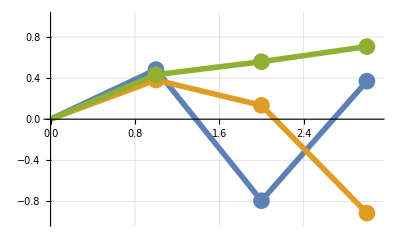

```mathematica
plt = Show[ListLinePlot[Table[Thread[{{0,1,2,3},Insert[NM,0,{{1,1},{2,1},{3,1}}][[k]]}],{k,3}],PlotStyle->{Thickness[0.01]},GridLines->Automatic,PlotRange->{{0,3.1},{-1,1}}],ListPlot[Table[Thread[{{1,2,3},NM[[k]]}],{k,3}],PlotStyle->PointSize[0.03],GridLines->Automatic]]
```